```mathematica
csvFiles=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"local"}]];
```

```mathematica
csvToDataset[csvFile_String]:=
Module[{rawData,keys,data,dataset},
rawData=Import[csvFile];
keys=rawData[[1]];
data=rawData[[2;;]];
dataset=Dataset[Association/@(Thread[Rule[keys,#]]&/@data)];

(* Process date and missings *)
(*dataset=dataset[{1->(<|#,"Date"->"1/1/1990"|>&)}];*)
dataset=dataset[All,{"Date"->(DateObject@DateList[{#,{"Month","Day","Year"}}]&)}];
dataset=dataset[All,All,If[#==="#N/A N/A",Missing[],#]&];
dataset
];
```

```mathematica
aapl=csvToDataset[First@csvFiles]
```

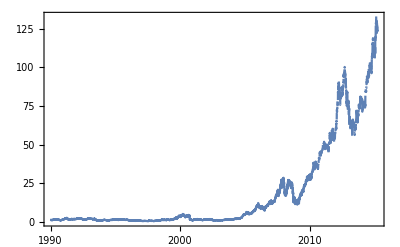

```mathematica
DateListPlot[aapl[All,{"Date","PX_LAST"}]]
```

```mathematica
datasets=Association[First@StringSplit[Last@StringSplit[#,"/"],"_"]->csvToDataset[#]&/@csvFiles];
```

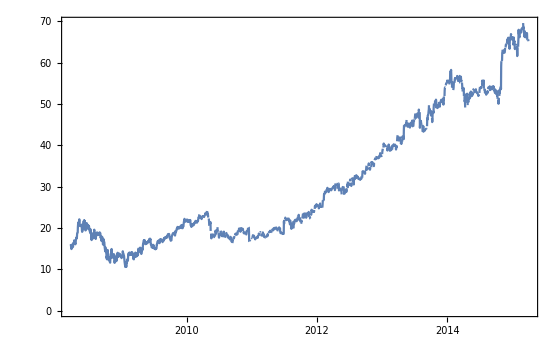

```mathematica
DateListPlot@datasets["V"][All,{"Date","PX_LAST"}]
```

```mathematica
datasets["V"][1]
```

```mathematica
{keys,
datasets["MSFT"][Count[_Missing],#]&/@keys/Length[datasets["MSFT"]]//N}//Transpose//TableForm
```

Date | 0.
PX_LAST | 0.0396981
PE_RATIO | 0.0396981
VOLATILITY_30D | 0.0396981
VOLATILITY_90D | 0.0396981
VOLATILITY_180D | 0.0396981
VOLATILITY_260D | 0.0396981
PX_VOLUME | 0.0448302
PX_TO_CASH_FLOW | 0.0584151
ADJUSTED_FINANCIALS_INDICATOR | 1.
GICS_SECTOR | 1.
GICS_INDUSTRY_GROUP | 1.
NUM_OF_EMPLOYEES | 0.0704906
PCT_FLT_SHARES_INSTITUTIONS | 0.960151

```mathematica
{x,y,z}[[;;-2]]
```

{x,y}

```mathematica
returns[{x,y,z}]
```

{(-x+y)/x,(-y+z)/y}

```mathematica
returns[datasets["MSFT"][All,"PX_LAST"]]
```

{0.0293643,-0.0244514,0.0152635,-0.0026903,-0.0276103,-0.0197454,6612,-0.00602991,-0.00582383,0.0244081 (-40.97+Missing[]),(40.96-Missing[])/Missing[],-0.00744629,0.00159882}
 |  |  |  |

```mathematica
DeleteCases[datasets["MSFT"][All,"PX_LAST"],Missing_]
```

```mathematica
datasets["MSFT"][All,"PX_LAST"]
```

```mathematica
msft=datasets["MSFT"];
```

```mathematica
cleanMsft=clean[msft]
```

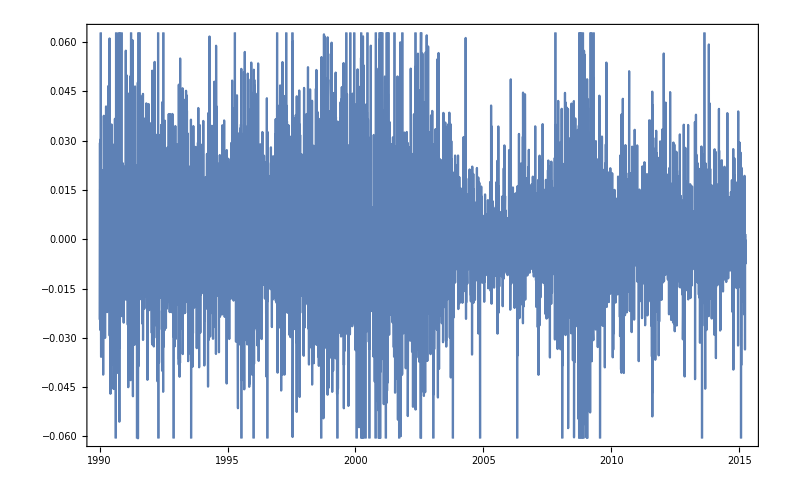

```mathematica
DateListPlot@Transpose@{Normal@cleanMsft[All,"Date"][[2;;]],returns[cleanMsft[All,"PX_LAST"]]}
```

```mathematica
(*FinancialData["MSFT","Volatility20Day",{{2015,01,01},{2015,04,05}}];*)
FinancialData["MSFT",{1990,01,01}]//Length
```

6364

```mathematica
FinancialData["MSFT","RawClose",{1990,01,01}]
```

{{{1990,1,2},88.75},{{1990,1,3},89.25},{{1990,1,4},91.87},{{1990,1,5},89.63},{{1990,1,8},91.},{{1990,1,9},90.75},{{1990,1,10},88.25},{{1990,1,11},86.5},{{1990,1,12},86.12},6346,{{2015,3,23},42.86},{{2015,3,24},42.9},{{2015,3,25},41.46},{{2015,3,26},41.21},{{2015,3,27},40.97},{{2015,3,30},40.96},{{2015,3,31},40.66},{{2015,4,1},40.72},{{2015,4,2},40.29}}
 |  |  |  |